{{a→-11/6,b→27/2,c→-89/3,d→21}}

21-(89 x)/3+(27 x^2)/2-(11 x^3)/6

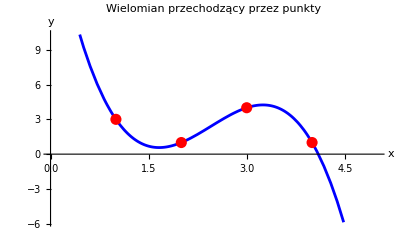

```mathematica
(*Zadanie 1*)
(*Definiujemy ogólny wielomian 3 go stopnia. ClearAll usuwa poprzednie przypisania z pamięci,by uniknąć błędów*)
ClearAll[cubic,a,b,c,d,x];
cubic[x_]:=a x^3+b x^2+c x+d;

punkty={{1,3},{2,1},{3,4},{4,1}};
rownania={cubic[1]==3,cubic[2]==1,cubic[3]==4,cubic[4]==1};
wspolczynniki=Solve[rownania,{a,b,c,d}]
gotowyWielomian[x_]=cubic[x]/. wspolczynniki[[1]]

Show[Plot[gotowyWielomian[x],{x,0,5},PlotStyle->Blue],ListPlot[punkty,PlotStyle->{Red,PointSize[0.02]}],PlotLabel->"Wielomian przechodzący przez punkty",AxesLabel->{"x","y"}]
```

```mathematica
(*Zadanie 2 (3 przypadki)*)
(*Symboliczne rozwiązanie przecięcia*)punktyPrzeciecia=Solve[x^2==2 x^2+a x+b,x]

(*Przypadek 1:Dwa punkty przecięcia (Delta>0).Wybieramy np.a=3, b=2 (Delta=9-8=1)*)
plot1=Plot[{x^2,2 x^2+3 x+2},{x,-4,2},PlotLabel->"Przypadek 1: 2 punkty (a=3, b=2)",PlotLegends->{"y = x^2","y = 2x^2 + 3x + 2"}];

(*Przypadek 2:Jeden punkt przecięcia/Styczność (Delta=0).Wybieramy np.a=4,b=4 (Delta=16-16=0)*)
plot2=Plot[{x^2,2 x^2+4 x+4},{x,-5,1},PlotLabel->"Przypadek 2: 1 punkt (a=4, b=4)"];

(*Przypadek 3:Brak punktów przecięcia (Delta<0).Wybieramy np.a=2,b=5 (Delta=4-20=-16)*)
plot3=Plot[{x^2,2 x^2+2 x+5},{x,-4,2},PlotLabel->"Przypadek 3: 0 punktów (a=2, b=5)"];

GraphicsColumn[{plot1,plot2,plot3},ImageSize->400]
```

{{x→1/2 (-a-√(a^2-4 b))},{x→1/2 (-a+√(a^2-4 b))}}

-Graphics-

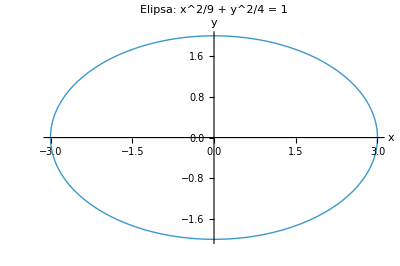

```mathematica
(*Zadanie 3a*)
(*a) Rysowanie elipsy*)ParametricPlot[{3 Cos[t],2 Sin[t]},{t,0,2 Pi},PlotLabel->"Elipsa: x^2/9 + y^2/4 = 1",AxesLabel->{"x","y"},PlotStyle->Thick]
```

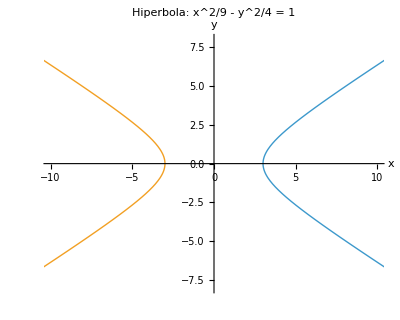

```mathematica
(*Zadanie 3b*)
(*b) Rysowanie hiperboli*)ParametricPlot[{{3 Cosh[t],2 Sinh[t]},{-3 Cosh[t],2 Sinh[t]}},{t,-2,2},PlotLabel->"Hiperbola: x^2/9 - y^2/4 = 1",AxesLabel->{"x","y"},PlotStyle->Thick,PlotRange->{{-10,10},{-8,8}}]
```